## vlpSol v1

Length scale α = D/V,  time scale β = D/V^2

```mathematica
α[ϵ1_,ϵ2_]=( 1/2 Dg Cg (1+ Exp[ϵ1-ϵ2]))/(Dg Cg (1- Exp[ϵ1-ϵ2]))
```

(1+ⅇ^(ϵ1-ϵ2))/(2 (1-ⅇ^(ϵ1-ϵ2)))

```mathematica
β[ϵ1_,ϵ2_, Cg_, Dg_]:=( 1/2 Dg Cg (1+ Exp[ϵ1-ϵ2]))/(Dg Cg (1- Exp[ϵ1-ϵ2]))^2
```

```mathematica
{α[3.99, 4],β[3.99,4., 0.1, 10]}
```

{100.001,10050.2}

```mathematica
Solve[ {(D β)/α^2==1, (β V)/α==1}, {α,β}]
```

{{α→D/V,β→D/V^2}}

```mathematica
vlpSol[xMax_, tMax_, r0_, s0_, Γ_, ϵ1_, ϵ2_]:= 
Module[
{pde, bc, ic, eqns, r, s},
(*
r[x_]:= - r0 Exp[- ϵ2 x];  (* reaction term r0 = c0 β = c0 D/V^2*)
s[x_]:= s0 Exp[-ϵ1 x];       (* source term s0 = β =D/V^2*)
*)

pde =    (* diffusion-advection-reaction-source partial differential equation *)
{
D[ p0[x,t], t] ==
D[ p0[x,t], {x,2}]-   D[p0[x,t], x]  + r0[x] p0[x,t]  + s0[x],

D[ p1[x,t], t] ==
D[ p1[x,t], {x,2}]-   D[p1[x,t], x]  + r1[x] p1[x,t]  + s1[x],

D[ p2[x,t], t] ==
D[ p2[x,t], {x,2}]-   D[p2[x,t], x]  + r2[x] p2[x,t]  + s2[x]

};

bc =    (* boundary condition in terms of  the current *)
{
(* p0 *)
- Derivative[1,0][p0][0,t] +  p0[0,t] == 0,
- Derivative[1,0][p0][xMax,t] +  p0[xMax,t] == Γ p0[xMax,t],

(* p1 *)


(* p2 *)


};

ic = 
{
p0[x,0]== 0,
p1[x,0]== 0,
p2[x,0]== 0
};

eqns= Join[ pde, bc,ic] ;

NDSolve[
eqns,
{p0,p1,p2},
{x,0,xMax},
{t,0.0, tMax}
]
]
```

## Reaction term:

## Increase of r_0 gives almost no change

```mathematica
xMax = 50;
tMax = 400;
```

```mathematica
dsolr0[0.1]= vlpSol[ 50,400 , 0.1, 1.5,1, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolr0[1.]= vlpSol[ 50,400 , 1., 1.5,1, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolr0[10.]= vlpSol[ 50,400 , 10., 1.5,1, 10, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
Manipulate[
Plot[ 
{p[x,t]/.dsolr0[0.1],
p[x,t]/.dsolr0[1.],
p[x,t]/.dsolr0[10.]
}, 
{x,0,xMax}, PlotRange-> {{0,xMax}, {0.005,0.02}},
PlotStyle->{Red, Darker@Green, Blue},
Frame->True,
FrameLabel->{"x","p"}],
{{t,tMax},0, tMax}
]
```

Plot::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

## Increase of ϵ2 gives practically no change

```mathematica
Timing[
dsolϵ2[3.6]= vlpSol[ 50,400 , 1., 1.,1.0, 3.5, 3.6 ]
]
```

{0.046875,{{p→InterpolatingFunction[…]}}}

```mathematica
dsolϵ2[4.0]= vlpSol[ 50,400 , 1., 1.,1., 3.5, 4.0 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolϵ2[4.5]= vlpSol[ 50,400 , 1., 1.,1., 3.5, 4.5 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
Manipulate[
LogPlot[ 
{p[x,t]/.dsolϵ2[3.6],
p[x,t]/.dsolϵ2[4.0], 
p[x,t]/.dsolϵ2[4.5] 
}, 
{x,0,xMax}, PlotRange-> {{0,xMax}, {5*^-4,0.5}},
PlotStyle->{Red, Darker@Green, Blue},
Frame->True,
FrameLabel->{"x","p"}],
{{t,tMax},0, tMax}
]
```

## Source term:

## Increase of s_0 increases the plateau value of p

```mathematica
dsols0[0.1]= vlpSol[ 50,400 , 1., 0.1,1, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsols0[1.]= vlpSol[ 50,400 , 1., 1.0,1, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsols0[10.]= vlpSol[ 50,400 , 1., 10.,1, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
Manipulate[
LogPlot[ 
{p[x,t]/.dsols0[0.1],
p[x,t]/.dsols0[1.],
p[x,t]/.dsols0[10.]
}, 
{x,0,xMax}, PlotRange-> {{0,xMax}, {5*^-4,0.2}},
PlotStyle->{Red, Darker@Green, Blue},
Frame->True,
FrameLabel->{"x","p"}],
{{t,tMax},0, tMax}
]
```

```mathematica
dataxMax={
{0.1,p[xMax,tMax]/.First@dsols0[0.1]},
{1.0,p[xMax,tMax]/.First@dsols0[1.]},
{10.,p[xMax,tMax]/.First@dsols0[10.]}
}
```

{{0.1,0.00117226},{1.,0.0117226},{10.,0.117226}}

```mathematica
ListPlot[data, Frame-> True, FrameLabel-> {"s0", "p(xMax,tMax)"}]
```

ListPlot::lpn: data is not a list of numbers or pairs of numbers.

ListPlot[data,Frame→True,FrameLabel→{s0,p(xMax,tMax)}]

```mathematica
datax0={
{0.1,p[0,tMax]/.First@dsols0[0.1]},
{1.0,p[0,tMax]/.First@dsols0[1.]},
{10.,p[0,tMax]/.First@dsols0[10.]}
}
```

{{0.1,0.000557196},{1.,0.00557196},{10.,0.0557196}}

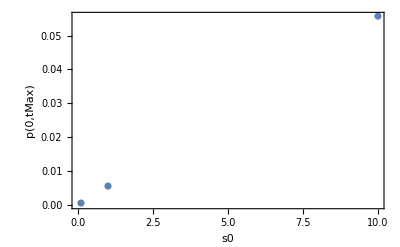

```mathematica
ListPlot[datax0, Frame-> True, FrameLabel-> {"s0", "p(0,tMax)"}]
```

## Increase of ϵ1 decreases the plateau of p

```mathematica
dsolϵ1[3.0]= vlpSol[ 50,400 , 1., 1.,1.0, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolϵ1[3.5]= vlpSol[ 50,400 , 1., 1.,1., 3.5, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolϵ1[3.99]= vlpSol[ 50,400 , 1., 1.,1., 3.99, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
Manipulate[
LogPlot[ 
{p[x,t]/.dsolϵ1[3.0],
p[x,t]/.dsolϵ1[3.5],
p[x,t]/.dsolϵ1[3.99]
}, 
{x,0,xMax}, PlotRange-> {{0,xMax}, {5*^-4,0.2}},
PlotStyle->{Red, Darker@Green, Blue},
Frame->True,
FrameLabel->{"x","p"}],
{{t,tMax},0, tMax}
]
```

{{3.,0.0117226},{3.5,0.00414057},{3.95,0.001622}}

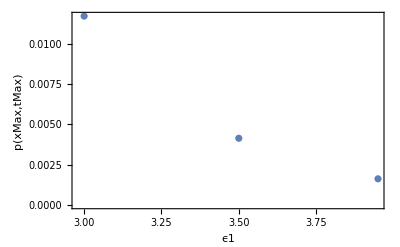

```mathematica
dataxMax={
{3.0,p[xMax,tMax]/.First@dsolϵ1[3.0]},
{3.5,p[xMax,tMax]/.First@dsolϵ1[3.5]},
{3.95,p[xMax,tMax]/.First@dsolϵ1[3.95]}
}

ListPlot[dataxMax, Frame-> True, FrameLabel-> {"ϵ1", "p(xMax,tMax)"}]
```

## Capsid extraction rate:

## Increase of Γ decreases p and its spatial derivative at x_max

```mathematica
dsolΓ[0.5]= vlpSol[ 50,400 , 1., 1.,0.5, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolΓ[1.]= vlpSol[ 50,400 , 1., 1.,1., 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
dsolΓ[1.5]= vlpSol[ 50,400 , 1., 1.,1.5, 3, 4 ]
```

{{p→InterpolatingFunction[…]}}

```mathematica
Manipulate[
LogPlot[ 
{p[x,t]/.dsolΓ[0.5],
p[x,t]/.dsolΓ[1.],
p[x,t]/.dsolΓ[1.5]
}, 
{x,0,xMax}, PlotRange-> {{0,xMax}, {5*^-4,0.2}},
PlotStyle->{Red, Darker@Green, Blue},
Frame->True,
FrameLabel->{"x","p"}],
{{t,tMax},0, tMax}
]
```

```mathematica
dataΓ={
{Γ,Γ p[xMax,tMax]}/.First@dsolΓ[0.5] /. Γ-> 0.5,
{Γ,Γ p[xMax,tMax]}/.First@dsolΓ[1.0] /. Γ-> 1.0,
{Γ,Γ p[xMax,tMax]}/.First@dsolΓ[1.5] /. Γ-> 1.5
}
```

{{0.5,0.0155561},{1.,0.0117226},{1.5,0.0108327}}

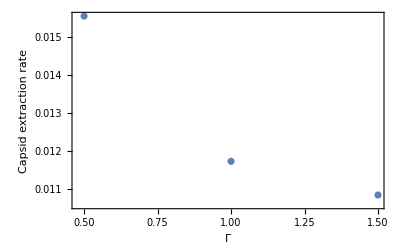

```mathematica
ListPlot[ dataΓ, Frame->True, FrameLabel-> {"Γ", "Capsid extraction rate"}]
```